Initial Graph:

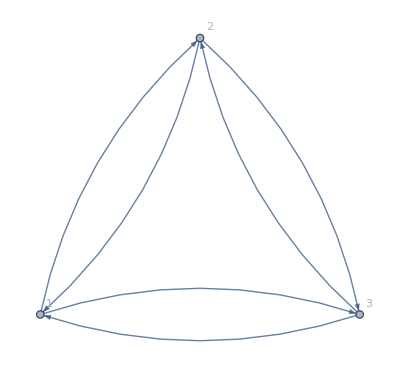

Frequency Vector: {{{1/(1-γ^2),γ/(1-γ^2),0},{1/(1-γ^3),γ/(1-γ^3),γ^2/(1-γ^3)},{1,γ/(1-γ^2),γ^2/(1-γ^2)},{1/(1-γ^2),0,γ/(1-γ^2)},{1/(1-γ^3),γ^2/(1-γ^3),γ/(1-γ^3)},{1,γ^2/(1-γ^2),γ/(1-γ^2)}},{{γ/(1-γ^2),1/(1-γ^2),0},{γ/(1-γ^2),1,γ^2/(1-γ^2)},{γ/(1-γ^3),1/(1-γ^3),γ^2/(1-γ^3)},{γ^2/(1-γ^3),1/(1-γ^3),γ/(1-γ^3)},{γ^2/(1-γ^2),1,γ/(1-γ^2)},{0,1/(1-γ^2),γ/(1-γ^2)}},{{γ/(1-γ^2),γ^2/(1-γ^2),1},{γ/(1-γ^3),γ^2/(1-γ^3),1/(1-γ^3)},{γ/(1-γ^2),0,1/(1-γ^2)},{γ^2/(1-γ^2),γ/(1-γ^2),1},{γ^2/(1-γ^3),γ/(1-γ^3),1/(1-γ^3)},{0,γ/(1-γ^2),1/(1-γ^2)}}}

#############################################################################################

Equation List: {r[1]/(1-γ^2)+(γ r[2])/(1-γ^2),r[1]/(1-γ^3)+(γ r[2])/(1-γ^3)+(γ^2 r[3])/(1-γ^3),r[1]+(γ r[2])/(1-γ^2)+(γ^2 r[3])/(1-γ^2),r[1]/(1-γ^2)+(γ r[3])/(1-γ^2),r[1]/(1-γ^3)+(γ^2 r[2])/(1-γ^3)+(γ r[3])/(1-γ^3),r[1]+(γ^2 r[2])/(1-γ^2)+(γ r[3])/(1-γ^2)}

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 1

Inequalities used: (1+2 γ≤√5&&(r[3]<r[1]||r[2]≤r[1])&&(r[3]<r[2]||r[2]>r[1]))||(1+2 γ>√5&&(r[2]≥r[1]||r[3]<r[2])&&(r[2]<r[1]||r[3]<r[1]))

Integration: -(5 γ)/(24 (-1+γ))

Measure: 1/3

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 2

Inequalities used: False

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 3

Inequalities used: r[1]<r[3]<r[2]

Integration: -(γ (3+2 γ))/(24 (-1+γ^2))

Measure: 1/6

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 4

Inequalities used: r[2]<r[1]&&r[3]>r[2]

Integration: -(5 γ)/(24 (-1+γ))

Measure: 1/3

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 5

Inequalities used: False

+++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++++

Current Frequency Index: 6

Inequalities used: r[2]>r[1]&&r[3]>r[2]

Integration: -(γ (3+2 γ))/(24 (-1+γ^2))

Measure: 1/6

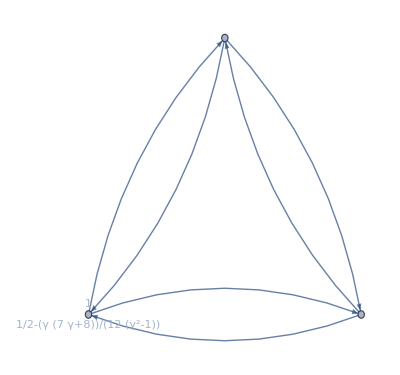
{0.681555,-Graphics-}

```mathematica
vertexAndNodes = {1->2, 1->3, 2->1, 2->3,3->1, 3->2};
vertexAndNodes = {1->2, 1->3, 1->4, 2->1, 2->3, 2->4, 3->1, 3->2, 3->4, 4->1, 4->2, 4->3};
(powerOfGraph[vertexAndNodes, "First", "Basic"]) //AbsoluteTiming
```